```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["mcpdict.json"];
```

```mathematica
pinyinAssoc=Association[FromCharacterCode[FromDigits[#⟦1⟧,16]]->(StringSplit[#⟦2⟧,","]⟦1⟧)&/@Select[({"unicode","pu"}/.#&/@data),#⟦2⟧≠""&]];
pinyinAssoc⟦"的"⟧="de";
pinyinRules=Normal[pinyinAssoc];
```

```mathematica
tones=StringCases[#,NumberString]&/@pinyinRules⟦All,2⟧/.{{t_String}:>ToExpression[t],{}:>0};
```

```mathematica
noTones=StringCases[#,LetterCharacter..]⟦1⟧&/@pinyinRules⟦All,2⟧;
```

```mathematica
ztrdReduced=StringReplace[noTones,{"zhi"->"zhii","chi"->"chii","shi"->"shii","ri"->"rii","zi"->"zii","ci"->"cii","si"->"sii","yi"->"i","wu"->"u","yu"->"v","yue"->"ve","yin"->"in","yun"->"vn","ying"->"ing","yuan"->"van","you"->"iu","wei"->"ui","wen"->"un","y"->"i","w"->"u"}];
```

```mathematica
vRestored=StringReplace[ztrdReduced,{"ju"->"jv","qu"->"qv","xu"->"xv"}];
```

```mathematica
consonants=StringCases[#,StartOfString~~("b"|"p"|"m"|"f"|"d"|"t"|"ng"|"n"|"l"|"g"|"k"|"h"|"j"|"q"|"x"|"zh"|"ch"|"sh"|"r"|"z"|"c"|"s")]&/@vRestored/.{{c_String}:>c,{}:>"0"};
```

```mathematica
consonantCounts=SortBy[Normal@Counts[consonants],Minus@*Last];
```

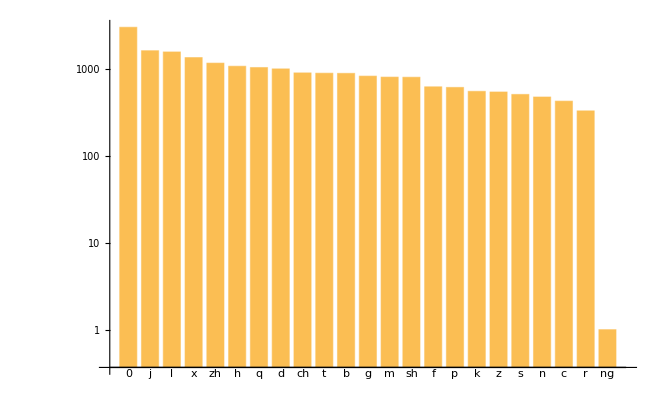

```mathematica
BarChart[consonantCounts⟦All,2⟧,ChartLabels->consonantCounts⟦All,1⟧,ScalingFunctions->"Log"]
```

```mathematica
rawConsonants=StringCases[#,StartOfString~~("b"|"p"|"m"|"f"|"d"|"t"|"ng"|"n"|"l"|"g"|"k"|"h"|"j"|"q"|"x"|"zh"|"ch"|"sh"|"r"|"z"|"c"|"s")]&/@vRestored/.{{c_String}:>c,{}:>""};
```

```mathematica
vowels=MapThread[StringReplace[#1,#2,1]&,{vRestored,#->""&/@rawConsonants}]/.{""->"0","io"->"iu","o"->"uo"};
```

```mathematica
vowelCounts=SortBy[Normal@Counts[vowels],Minus@*Last];
```

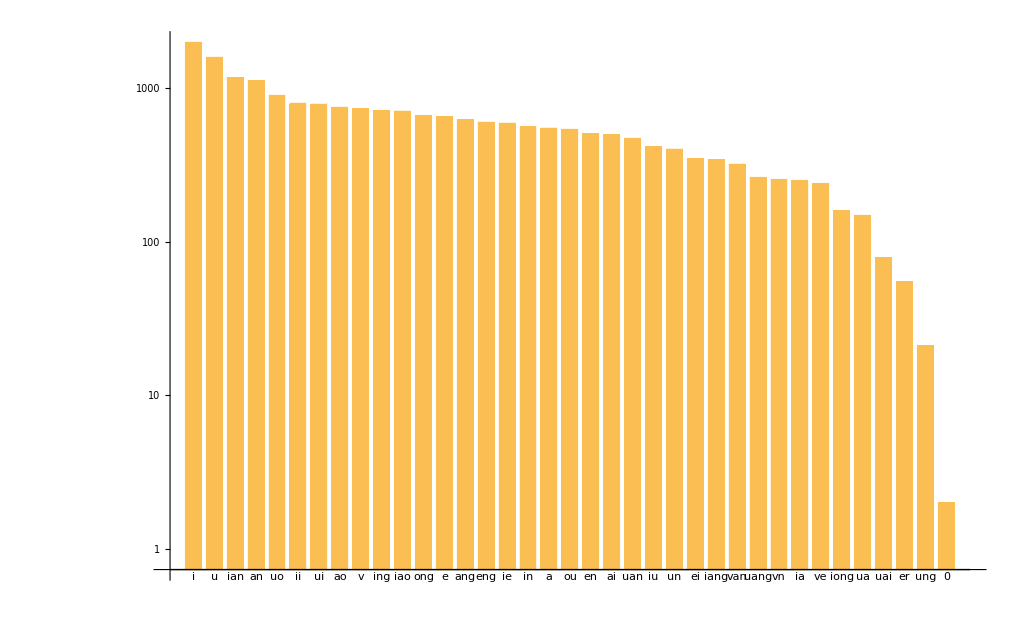

```mathematica
BarChart[vowelCounts⟦All,2⟧,ChartLabels->vowelCounts⟦All,1⟧,ScalingFunctions->"Log"]
```

```mathematica
hu=vowels/.{"a"|"e"|"ii"|"ai"|"ei"|"ao"|"ou"|"an"|"en"|"ang"|"eng"|"ong"|"er"->"kai","ia"|"ie"|"i"|"iao"|"iu"|"ian"|"in"|"iang"|"ing"|"iong"->"qi","ua"|"uo"|"u"|"uai"|"ui"|"uan"|"un"|"uang"|"ung"|"0"->"he","ve"|"v"|"van"|"vn"->"cuo"};
```

```mathematica
codas=vowels/.{"a"|"e"|"ii"|"ia"|"ie"|"ua"|"uo"|"0"|"ve"->"0","ai"|"ei"|"i"|"uai"|"ui"->"i","ao"|"ou"|"iao"|"iu"|"u"|"v"->"u","an"|"en"|"ian"|"in"|"uan"|"un"|"van"|"vn"->"n","ang"|"eng"|"ong"|"iang"|"ing"|"iong"|"uang"|"ung"->"ng","er"->"r"};
```

```mathematica
mu=vowels/.{"ong"|"ung"|"iong"->"dong","eng"|"ing"->"geng","ang"|"iang"|"uang"->"tang","ei"|"ui"->"wei","i"->"qi","er"->"er","ii"->"zhi","v"->"yu","u"|"0"->"mu","ai"|"uai"->"kai","en"|"in"|"un"|"vn"->"hen","an"|"uan"|"ian"|"van"->"han","ao"|"iao"->"hao","o"|"uo"->"bo","e"->"ge","ie"|"ve"->"jie","a"|"ia"|"ua"->"ma","ou"|"iu"->"hou"};
```

```mathematica
pinyinCounts=SortBy[Normal[Counts[pinyinRules⟦All,2⟧]],Minus@*Last];
```

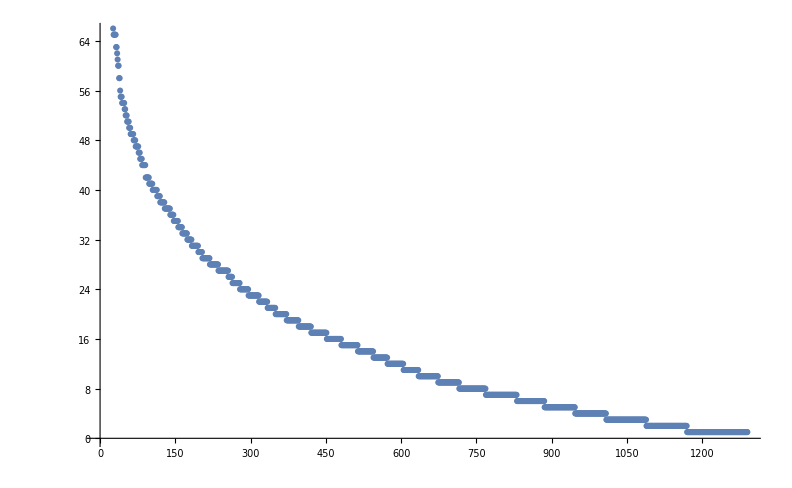

```mathematica
ListPlot[pinyinCounts⟦All,2⟧]
```

```mathematica
pinyinCounts⟦1;;10⟧
```

{yi4→202,li4→140,xi1→136,yu4→131,zhi4→124,bi4→123,ji4→110,yu2→97,ji1→96,qi2→95}

```mathematica
withTones={"ā","āi","ái","ǎi","ài","ān","án","ǎn","àn","āng","áng","àng","āo","áo","ǎo","ào","bā","bá","bǎ","bà","bāi","bái","bǎi","bài","bān","bǎn","bàn","bāng","bǎng","bàng","bāo","báo","bǎo","bào","bei","bēi","běi","bèi","bēn","běn","bèn","bēng","béng","běng","bèng","bī","bí","bǐ","bì","biān","biǎn","biàn","biāo","biáo","biǎo","biào","biē","bié","biè","bīn","bìn","bīng","bǐng","bìng","bo","bō","bó","bǒ","bò","bū","bú","bǔ","bù","būn","cā","cǎ","cà","cāi","cái","cǎi","cài","cān","cán","cǎn","càn","cāng","cáng","càng","cāo","cáo","cǎo","cào","cè","cēn","cén","cēng","céng","cèng","chā","chá","chǎ","chà","chāi","chái","chǎi","chài","chān","chán","chǎn","chàn","chāng","cháng","chǎng","chàng","chāo","cháo","chǎo","chào","chē","chě","chè","chēn","chén","chěn","chèn","chēng","chéng","chěng","chèng","chi","chī","chí","chǐ","chì","chōng","chóng","chǒng","chòng","chou","chōu","chóu","chǒu","chòu","chū","chú","chǔ","chù","chuāi","chuái","chuǎi","chuài","chuān","chuán","chuǎn","chuàn","chuāng","chuáng","chuǎng","chuàng","chuī","chuí","chūn","chún","chǔn","chuō","chuò","cī","cí","cǐ","cì","cōng","cóng","còng","còu","cū","cú","cù","cuān","cuán","cuàn","cuī","cuǐ","cuì","cūn","cún","cǔn","cùn","cuō","cuó","cuǒ","cuò","da","dā","dá","dǎ","dà","dāi","dǎi","dài","dān","dǎn","dàn","dāng","dǎng","dàng","dāo","dáo","dǎo","dào","de","dē","dé","dèn","dēng","děng","dèng","dī","dí","dǐ","dì","diǎ","diān","diǎn","diàn","diāo","diǎo","diào","diē","dié","diè","dīng","dǐng","dìng","diū","dōng","dǒng","dòng","dōu","dóu","dǒu","dòu","dū","dú","dǔ","dù","duān","duǎn","duàn","duī","duǐ","duì","dūn","dǔn","dùn","duō","duó","duǒ","duò","ē","é","ě","è","ēi","èi","ēn","ěn","èn","ēng","ér","ěr","èr","fā","fá","fǎ","fà","fān","fán","fǎn","fàn","fāng","fáng","fǎng","fàng","fēi","féi","fěi","fèi","fēn","fén","fěn","fèn","fēng","féng","fěng","fèng","fiào","fó","fóu","fǒu","fū","fú","fǔ","fù","gā","gá","gǎ","gà","gāi","gǎi","gài","gān","gǎn","gàn","gāng","gǎng","gàng","gāo","gǎo","gào","gē","gé","gě","gè","gěi","gēn","gén","gèn","gēng","gěng","gèng","gōng","gǒng","gòng","gōu","gǒu","gòu","gū","gǔ","gù","guā","guǎ","guà","guāi","guái","guǎi","guài","guān","guǎn","guàn","guāng","guǎng","guàng","guī","guǐ","guì","gǔn","gùn","guō","guó","guǒ","guò","hā","hāi","hái","hǎi","hài","hān","hán","hǎn","hàn","hāng","háng","hàng","hāo","háo","hǎo","hào","hē","hé","hè","hēi","hén","hěn","hèn","hēng","héng","hèng","hōng","hóng","hǒng","hòng","hōu","hóu","hǒu","hòu","hū","hú","hǔ","hù","huā","huá","huà","huái","huài","huān","huán","huǎn","huàn","huāng","huáng","huǎng","huàng","huī","huí","huǐ","huì","hūn","hún","hùn","huō","huó","huǒ","huò","jī","jí","jǐ","jì","jiā","jiá","jiǎ","jià","jiān","jiǎn","jiàn","jiāng","jiǎng","jiàng","jiāo","jiáo","jiǎo","jiào","jiē","jié","jiě","jiè","jīn","jǐn","jìn","jīng","jǐng","jìng","jiōng","jiǒng","jiū","jiǔ","jiù","jū","jú","jǔ","jù","juān","juǎn","juàn","juē","jué","jūn","jùn","kā","kǎ","kāi","kǎi","kài","kān","kǎn","kàn","kāng","káng","kàng","kāo","kǎo","kào","kē","ké","kě","kè","kēi","kěn","kèn","kēng","kōng","kǒng","kòng","kōu","kǒu","kòu","kū","kǔ","kù","kuā","kuǎ","kuà","kuǎi","kuài","kuān","kuǎn","kuāng","kuáng","kuǎng","kuàng","kuī","kuí","kuǐ","kuì","kūn","kǔn","kùn","kuò","la","lā","lá","lǎ","là","lái","lǎi","lài","lán","lǎn","làn","lāng","láng","lǎng","làng","lāo","láo","lǎo","lào","lè","lei","léi","lěi","lèi","léng","lěng","lèng","li","lí","lǐ","lì","lián","liǎn","liàn","liáng","liǎng","liàng","liāo","liáo","liǎo","liào","liě","liè","līn","lín","lǐn","lìn","líng","lǐng","lìng","liū","liú","liǔ","liù","lóng","lǒng","lòng","lóu","lǒu","lòu","lū","lú","lǔ","lù","luán","luǎn","luàn","lūn","lún","lǔn","lùn","luō","luó","luǒ","luò","lǘ","lǚ","lǜ","lüè","m2","mā","má","mǎ","mà","mái","mǎi","mài","mān","mán","mǎn","màn","māng","máng","mǎng","māo","máo","mǎo","mào","mē","mè","méi","měi","mèi","mēn","mén","mèn","mēng","méng","měng","mèng","mī","mí","mǐ","mì","mián","miǎn","miàn","miāo","miáo","miǎo","miào","miē","miè","mín","mǐn","míng","mǐng","mìng","miù","mō","mó","mǒ","mò","mōu","móu","mǒu","mú","mǔ","mù","ná","nǎ","nà","nái","nǎi","nài","nān","nán","nǎn","nàn","nāng","náng","nǎng","nàng","nāo","náo","nǎo","nào","nè","něi","nèi","nèn","néng","ng4","nī","ní","nǐ","nì","niān","nián","niǎn","niàn","niáng","niàng","niǎo","niào","niē","nié","niè","nín","nǐn","níng","nǐng","nìng","niū","niú","niǔ","nóng","nǒng","nòng","nóu","nòu","nú","nǔ","nù","nuán","nuǎn","nún","nuó","nuò","nǚ","nǜ","nüè","ō","ó","ōu","ǒu","òu","pā","pá","pà","pāi","pái","pài","pān","pán","pǎn","pàn","pāng","páng","pǎng","pàng","pāo","páo","pǎo","pào","pēi","péi","pěi","pèi","pēn","pén","pěn","pèn","pēng","péng","pěng","pèng","pī","pí","pǐ","pì","piān","pián","piǎn","piàn","piāo","piáo","piǎo","piào","piē","piě","piè","pīn","pín","pǐn","pìn","pīng","píng","pǐng","pō","pó","pǒ","pò","pōu","póu","pǒu","pū","pú","pǔ","pù","qī","qí","qǐ","qì","qiā","qiǎ","qià","qiān","qián","qiǎn","qiàn","qiāng","qiáng","qiǎng","qiàng","qiāo","qiáo","qiǎo","qiào","qiē","qié","qiě","qiè","qīn","qín","qǐn","qìn","qīng","qíng","qǐng","qìng","qióng","qiū","qiú","qiǔ","qū","qú","qǔ","qù","quān","quán","quǎn","quàn","quē","qué","què","qūn","qún","rán","rǎn","ráng","rǎng","ràng","ráo","rǎo","rào","rě","rè","rén","rěn","rèn","rēng","réng","rì","róng","rǒng","ròng","róu","rǒu","ròu","rū","rú","rǔ","rù","ruán","ruǎn","ruí","ruǐ","ruì","rún","rùn","ruó","ruò","sā","sǎ","sà","sāi","sǎi","sài","sān","sǎn","sàn","sāng","sǎng","sāo","sǎo","sào","sē","sè","sēn","sēng","shā","shá","shǎ","shà","shāi","shài","shān","shǎn","shàn","shāng","shǎng","shàng","shāo","sháo","shǎo","shào","shē","shé","shě","shè","shēn","shén","shěn","shèn","shēng","shéng","shěng","shèng","shī","shí","shǐ","shì","shōu","shǒu","shòu","shū","shú","shǔ","shù","shuā","shuǎ","shuà","shuāi","shuǎi","shuài","shuān","shuàn","shuāng","shuǎng","shuàng","shuí","shuǐ","shuì","shǔn","shùn","shuō","shuò","sī","sǐ","sì","sōng","sǒng","sòng","sōu","sǒu","sòu","sū","sú","sù","suān","suǎn","suàn","suī","suí","suǐ","suì","sūn","sǔn","suō","suǒ","suò","tā","tǎ","tà","tāi","tái","tài","tān","tán","tǎn","tàn","tāng","táng","tǎng","tàng","tāo","táo","tǎo","tào","tè","tēng","téng","tèng","tī","tí","tǐ","tì","tiān","tián","tiǎn","tiàn","tiāo","tiáo","tiǎo","tiào","tiē","tiě","tiè","tīng","tíng","tǐng","tōng","tóng","tǒng","tòng","tōu","tóu","tǒu","tòu","tū","tú","tǔ","tù","tuān","tuán","tuǎn","tuàn","tuī","tuí","tuǐ","tuì","tūn","tún","tǔn","tuō","tuó","tuǒ","tuò","wā","wá","wǎ","wà","wāi","wǎi","wài","wān","wán","wǎn","wàn","wāng","wáng","wǎng","wàng","wēi","wéi","wěi","wèi","wēn","wén","wěn","wèn","wēng","wěng","wèng","wō","wǒ","wò","wū","wú","wǔ","wù","xī","xí","xǐ","xì","xiā","xiá","xiǎ","xià","xiān","xián","xiǎn","xiàn","xiāng","xiáng","xiǎng","xiàng","xiāo","xiáo","xiǎo","xiào","xiē","xié","xiě","xiè","xīn","xín","xǐn","xìn","xīng","xíng","xǐng","xìng","xiōng","xióng","xiǒng","xiòng","xiū","xiú","xiǔ","xiù","xū","xú","xǔ","xù","xuān","xuán","xuǎn","xuàn","xuē","xué","xuě","xuè","xūn","xún","xùn","yā","yá","yǎ","yà","yān","yán","yǎn","yàn","yāng","yáng","yǎng","yàng","yāo","yáo","yǎo","yào","yē","yé","yě","yè","yī","yí","yǐ","yì","yīn","yín","yǐn","yìn","yīng","yíng","yǐng","yìng","yō","yōng","yóng","yǒng","yòng","yōu","yóu","yǒu","yòu","yū","yú","yǔ","yù","yuān","yuán","yuǎn","yuàn","yuē","yuě","yuè","yūn","yún","yǔn","yùn","zā","zá","zǎ","zāi","zǎi","zài","zān","zán","zǎn","zàn","zāng","zǎng","zàng","zāo","záo","zǎo","zào","zé","zè","zéi","zěn","zèn","zēng","zèng","zhā","zhá","zhǎ","zhà","zhāi","zhái","zhǎi","zhài","zhān","zhán","zhǎn","zhàn","zhāng","zhǎng","zhàng","zhāo","zhǎo","zhào","zhē","zhé","zhě","zhè","zhēn","zhěn","zhèn","zhēng","zhěng","zhèng","zhī","zhí","zhǐ","zhì","zhōng","zhǒng","zhòng","zhōu","zhóu","zhǒu","zhòu","zhū","zhú","zhǔ","zhù","zhuā","zhuǎi","zhuài","zhuān","zhuǎn","zhuàn","zhuāng","zhuàng","zhuī","zhuǐ","zhuì","zhūn","zhǔn","zhùn","zhuō","zhuó","zī","zí","zǐ","zì","zōng","zǒng","zòng","zōu","zǒu","zòu","zū","zú","zǔ","zuān","zuǎn","zuàn","zuī","zuǐ","zuì","zūn","zǔn","zùn","zuo","zuō","zuó","zuǒ","zuò"};
```

```mathematica
pinyins=pinyinRules⟦All,2⟧/.MapThread[Rule,{Union[pinyinRules⟦All,2⟧],withTones}];
```

```mathematica
Export["rimes.json",MapThread[Rule,{pinyinRules⟦All,1⟧,Transpose[{pinyins,consonants,hu,vowels,codas,mu,tones}]}],"Compact"->True]
```

rimes.json